# PCA- raman data (practice)

## Import data

```mathematica
MGH1:=Import["/Users/naomi/Documents/naomi/PCA raman data/from Igor HUCP43 vs MGH/Best 10_MGH_9may_cell ref_ascii/MGH_5x40aq_1a'_cell ref.asc"]
MGH2:=Import["/Users/naomi/Documents/naomi/PCA raman data/from Igor HUCP43 vs MGH/Best 10_MGH_9may_cell ref_ascii/MGH_10x10_1a_cell ref_ie cell minus backgr.asc"]
MGH3:=Import["/Users/naomi/Documents/naomi/PCA raman data/from Igor HUCP43 vs MGH/Best 10_MGH_9may_cell ref_ascii/MGH_10x20aq_3a_cell ref.asc"]
MGH4:=Import["/Users/naomi/Documents/naomi/PCA raman data/from Igor HUCP43 vs MGH/Best 10_MGH_9may_cell ref_ascii/MGH_10x20aq_4a_cell ref.asc"]
MGH5:=Import["/Users/naomi/Documents/naomi/PCA raman data/from Igor HUCP43 vs MGH/Best 10_MGH_9may_cell ref_ascii/MGH_10x20aq_5c_cell ref.asc"]
MGH6:=Import["/Users/naomi/Documents/naomi/PCA raman data/from Igor HUCP43 vs MGH/Best 10_MGH_9may_cell ref_ascii/MGH_10x20aq_8c_cell ref.asc"]
MGH7:=
Import["/Users/naomi/Documents/naomi/PCA raman data/from Igor HUCP43 vs MGH/Best 10_MGH_9may_cell ref_ascii/MGH_10x20aq_10c_cell ref.asc"]
MGH8:=Import["/Users/naomi/Documents/naomi/PCA raman data/from Igor HUCP43 vs MGH/Best 10_MGH_9may_cell ref_ascii/MGH_10x20aq_14c_cell ref.asc"]
MGH9:=Import["/Users/naomi/Documents/naomi/PCA raman data/from Igor HUCP43 vs MGH/Best 10_MGH_9may_cell ref_ascii/MGH_10x20aq_19c_cell ref.asc"]
```

```mathematica
HUC1:=Import["/Users/naomi/Documents/naomi/PCA raman data/from Igor HUCP43 vs MGH/Best 10_HUCP43_15may_cell ref_ascii/HUCP43_15may_2c_cell ref.asc"]
HUC2:=Import["/Users/naomi/Documents/naomi/PCA raman data/from Igor HUCP43 vs MGH/Best 10_HUCP43_15may_cell ref_ascii/HUCP43_15may_5c_cell ref.asc"]
HUC3:=Import["/Users/naomi/Documents/naomi/PCA raman data/from Igor HUCP43 vs MGH/Best 10_HUCP43_15may_cell ref_ascii/HUCP43_15may_6c_cell ref.asc"]
HUC4:=Import["/Users/naomi/Documents/naomi/PCA raman data/from Igor HUCP43 vs MGH/Best 10_HUCP43_15may_cell ref_ascii/HUCP43_15may_7c_cell ref.asc"]
HUC5:=Import["/Users/naomi/Documents/naomi/PCA raman data/from Igor HUCP43 vs MGH/Best 10_HUCP43_15may_cell ref_ascii/HUCP43_15may_8c_cell ref.asc"]
HUC6:=Import["/Users/naomi/Documents/naomi/PCA raman data/from Igor HUCP43 vs MGH/Best 10_HUCP43_15may_cell ref_ascii/HUCP43_15may_10c_cell ref.asc"]
HUC7:=Import["/Users/naomi/Documents/naomi/PCA raman data/from Igor HUCP43 vs MGH/Best 10_HUCP43_15may_cell ref_ascii/HUCP43_15may_12c_cell ref.asc"]
HUC8:=Import["/Users/naomi/Documents/naomi/PCA raman data/from Igor HUCP43 vs MGH/Best 10_HUCP43_15may_cell ref_ascii/HUCP43_15may_15c_cell ref.asc"]
HUC9:=Import["/Users/naomi/Documents/naomi/PCA raman data/from Igor HUCP43 vs MGH/Best 10_HUCP43_15may_cell ref_ascii/HUCP43_15may_16c_cell ref.asc"]
```

## Graph of data and averages

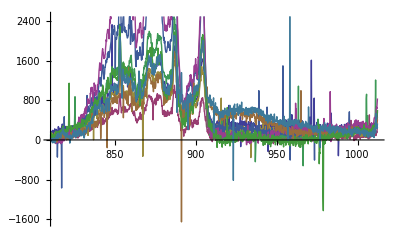

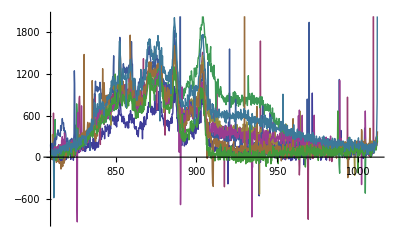

```mathematica
ListLinePlot[{MGH1,MGH2,MGH3,MGH4,MGH5,MGH6,MGH7,MGH8,MGH9}]
ListLinePlot[{HUC1,HUC2,HUC3,HUC4,HUC5,HUC6,HUC7,HUC8,HUC9}]
```

```mathematica
averagedMGH=Table[{MGH1[[i,1]],Mean[{MGH1[[i,2]],MGH2[[i,2]],MGH3[[i,2]],MGH4[[i,2]],MGH5[[i,2]],MGH6[[i,2]],MGH7[[i,2]],MGH8[[i,2]],MGH9[[i,2]]}]},{i,Length[MGH1]}];
```

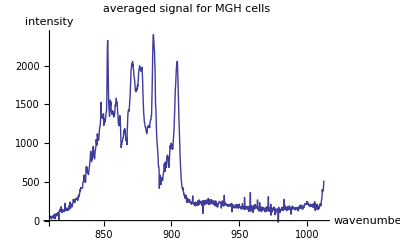

```mathematica
ListLinePlot[averagedMGH,AxesLabel->{"wavenumber","intensity"},PlotLabel->"averaged signal for MGH cells"]
```

```mathematica
averagedHUV=Table[{HUC1[[j,1]],Mean[{HUC1[[j,2]],HUC2[[j,2]],HUC3[[j,2]],HUC4[[j,2]],HUC5[[j,2]],HUC6[[j,2]],HUC7[[j,2]],HUC8[[j,2]],HUC9[[j,2]]}]},{j,Length[HUC1]}]
```

{{809.792,68},{809.994,166/3},{810.196,490/9},{810.398,217/3},{810.6,61},{810.802,706/9},{811.004,907/9},{811.206,547/9},{811.408,602/9},{811.61,1055/9},{811.812,62/3},{812.013,191/9},{812.215,698/9},{812.417,730/9},{812.619,1267/9},{812.821,464/9},{813.023,791/9},{813.225,697/9},{813.427,757/9},{813.628,721/9},{813.83,895/9},{814.032,959/9},{814.234,911/9},{814.436,1022/9},{814.637,758/9},{814.839,1061/9},{815.041,814/9},{815.243,256/3},{815.445,965/9},{815.646,859/9},{815.848,794/9},{816.05,707/9},{816.252,565/9},{816.453,944/9},{816.655,1069/9},{816.857,389/3},{817.059,1250/9},{817.26,1108/9},{817.462,1316/9},{817.664,1390/9},{817.865,1319/9},{818.067,1192/9},{818.269,352/3},{818.47,1136/9},{818.672,1075/9},{818.874,1349/9},{819.075,1042/9},{819.277,425/3},{819.479,331/3},{819.68,340/3},{819.882,979/9},{820.083,1040/9},{820.285,1153/9},{820.487,1226/9},{820.688,820/9},{820.89,1175/9},{821.091,326/3},{821.293,136},{821.495,135},{821.696,1333/9},{821.898,1162/9},{822.099,1156/9},{822.301,1238/9},{822.502,1298/9},{822.704,1312/9},{822.905,1250/9},{823.107,1223/9},{823.308,1261/9},{823.51,1382/9},{823.711,1168/9},{823.913,1432/9},{824.114,1396/9},{824.316,532/3},{824.517,2653/9},{824.718,2120/9},{824.92,1411/9},{825.121,1648/9},{825.323,1426/9},{825.524,1478/9},{825.726,445/3},{825.927,277},{826.128,1154/9},{826.33,413/9},{826.531,2126/9},{826.732,677/3},{826.934,1751/9},{827.135,1769/9},{827.337,2171/9},{827.538,2675/9},{827.739,815/3},{827.941,2060/9},{828.142,1925/9},{828.343,1805/9},{828.544,1775/9},{828.746,235},{828.947,2567/9},{829.148,2278/9},{829.35,2093/9},{829.551,695/3},{829.752,619/3},{829.953,2050/9},{830.155,2035/9},{830.356,2098/9},{830.557,3274/9},{830.758,1822/9},{830.959,2236/9},{831.161,1844/9},{831.362,713/3},{831.563,2057/9},{831.764,731/3},{831.965,2642/9},{832.167,2326/9},{832.368,2288/9},{832.569,2791/9},{832.77,2908/9},{832.971,289},{833.172,2876/9},{833.373,1006/3},{833.575,2849/9},{833.776,310},{833.977,2920/9},{834.178,920/3},{834.379,3014/9},{834.58,3248/9},{834.781,3251/9},{834.982,3472/9},{835.183,3616/9},{835.384,1108/3},{835.585,4067/9},{835.786,3995/9},{835.987,3191/9},{836.188,1178/3},{836.389,1298/3},{836.59,1534/3},{836.791,519},{836.992,4744/9},{837.193,5066/9},{837.394,5423/9},{837.595,1556/3},{837.796,540},{837.997,4681/9},{838.198,4490/9},{838.399,4606/9},{838.6,4912/9},{838.801,524},{839.002,4984/9},{839.203,4975/9},{839.404,1657/3},{839.604,5191/9},{839.805,5323/9},{840.006,1904/3},{840.207,1913/3},{840.408,1829/3},{840.609,1631/3},{840.81,5374/9},{841.01,5470/9},{841.211,1787/3},{841.412,1855/3},{841.613,5608/9},{841.814,5831/9},{842.014,2077/3},{842.215,1862/3},{842.416,5663/9},{842.617,1688/3},{842.818,5395/9},{843.018,5317/9},{843.219,5104/9},{843.42,1802/3},{843.62,5690/9},{843.821,5632/9},{844.022,5851/9},{844.223,668},{844.423,6298/9},{844.624,2038/3},{844.825,6410/9},{845.025,6239/9},{845.226,2083/3},{845.427,6653/9},{845.627,6131/9},{845.828,6292/9},{846.029,694},{846.229,2158/3},{846.43,2104/3},{846.631,6784/9},{846.831,6821/9},{847.032,6640/9},{847.232,2407/3},{847.433,7420/9},{847.633,2444/3},{847.834,835},{848.035,7799/9},{848.235,7666/9},{848.436,7598/9},{848.636,7945/9},{848.837,8182/9},{849.037,7802/9},{849.238,2506/3},{849.438,865},{849.639,7756/9},{849.839,8174/9},{850.04,2458/3},{850.24,7334/9},{850.441,2447/3},{850.641,7240/9},{850.842,7390/9},{851.042,7703/9},{851.242,2575/3},{851.443,7871/9},{851.643,2618/3},{851.844,2680/3},{852.044,2926/3},{852.244,10243/9},{852.445,11654/9},{852.645,1311},{852.846,11390/9},{853.046,3430/3},{853.246,8678/9},{853.447,2834/3},{853.647,2768/3},{853.847,7946/9},{854.048,7720/9},{854.248,8056/9},{854.448,8534/9},{854.649,8903/9},{854.849,8752/9},{855.049,8371/9},{855.249,8443/9},{855.45,901},{855.65,8138/9},{855.85,8311/9},{856.05,8192/9},{856.251,905},{856.451,2701/3},{856.651,7972/9},{856.851,8122/9},{857.052,2683/3},{857.252,8083/9},{857.452,8125/9},{857.652,8039/9},{857.852,8195/9},{858.052,2705/3},{858.253,8603/9},{858.453,8947/9},{858.653,8879/9},{858.853,2993/3},{859.053,9902/9},{859.253,9964/9},{859.453,3094/3},{859.653,9011/9},{859.853,9122/9},{860.054,8747/9},{860.254,8360/9},{860.454,874},{860.654,7777/9},{860.854,7376/9},{861.054,827},{861.254,828},{861.454,880},{861.654,7862/9},{861.854,7985/9},{862.054,7355/9},{862.254,6863/9},{862.454,6979/9},{862.654,2117/3},{862.854,2077/3},{863.054,6277/9},{863.254,6277/9},{863.454,2113/3},{863.654,6595/9},{863.854,6608/9},{864.053,6719/9},{864.253,6958/9},{864.453,6985/9},{864.653,6974/9},{864.853,808},{865.053,7402/9},{865.253,7547/9},{865.453,2494/3},{865.653,7562/9},{865.852,7078/9},{866.052,7270/9},{866.252,2375/3},{866.452,7022/9},{866.652,7105/9},{866.851,2453/3},{867.051,840},{867.251,8239/9},{867.451,8087/9},{867.651,8402/9},{867.85,2954/3},{868.05,932},{868.25,2821/3},{868.45,8057/9},{868.649,8672/9},{868.849,2902/3},{869.049,9151/9},{869.248,9341/9},{869.448,9832/9},{869.648,3335/3},{869.847,10426/9},{870.047,10774/9},{870.247,10951/9},{870.446,10994/9},{870.646,11269/9},{870.846,11297/9},{871.045,11060/9},{871.245,11057/9},{871.445,10618/9},{871.644,10801/9},{871.844,10619/9},{872.043,3352/3},{872.243,3401/3},{872.443,10069/9},{872.642,3286/3},{872.842,9928/9},{873.041,3272/3},{873.241,9778/9},{873.44,3274/3},{873.64,9775/9},{873.839,9941/9},{874.039,3347/3},{874.238,3433/3},{874.438,10277/9},{874.637,3350/3},{874.837,10447/9},{875.036,3512/3},{875.236,10609/9},{875.435,10570/9},{875.634,3667/3},{875.834,11032/9},{876.033,1237},{876.233,10867/9},{876.432,11126/9},{876.632,3707/3},{876.831,11164/9},{877.03,10801/9},{877.23,10340/9},{877.429,3425/3},{877.628,11437/9},{877.828,1248},{878.027,3719/3},{878.226,3572/3},{878.426,3455/3},{878.625,9946/9},{878.824,9388/9},{879.024,3041/3},{879.223,8734/9},{879.422,944},{879.621,924},{879.821,894},{880.02,2639/3},{880.219,8261/9},{880.418,8080/9},{880.618,7451/9},{880.817,8209/9},{881.016,887},{881.215,7870/9},{881.414,7630/9},{881.614,2587/3},{881.813,7507/9},{882.012,858},{882.211,2653/3},{882.41,2542/3},{882.609,2654/3},{882.808,2555/3},{883.008,7658/9},{883.207,7787/9},{883.406,2672/3},{883.605,7751/9},{883.804,2665/3},{884.003,2689/3},{884.202,8315/9},{884.401,8167/9},{884.6,8464/9},{884.799,2785/3},{884.998,8521/9},{885.197,9130/9},{885.396,1073},{885.595,1187},{885.794,11912/9},{885.993,12401/9},{886.192,4379/3},{886.391,13231/9},{886.59,13141/9},{886.789,12995/9},{886.988,4094/3},{887.187,4060/3},{887.386,11654/9},{887.585,11035/9},{887.784,1173},{887.983,9680/9},{888.182,8867/9},{888.381,8207/9},{888.579,8005/9},{888.778,7189/9},{888.977,7169/9},{889.176,6955/9},{889.375,683},{889.574,6217/9},{889.773,6223/9},{889.971,10762/9},{890.17,4418/9},{890.369,4433/9},{890.568,5441/9},{890.767,1655/3},{890.965,5270/9},{891.164,5947/9},{891.363,1777/3},{891.562,5024/9},{891.76,548},{891.959,573},{892.158,5077/9},{892.356,5020/9},{892.555,1579/3},{892.754,4874/9},{892.953,1531/3},{893.151,5150/9},{893.35,5279/9},{893.549,5183/9},{893.747,1739/3},{893.946,5347/9},{894.144,5480/9},{894.343,5503/9},{894.542,5996/9},{894.74,1802/3},{894.939,5807/9},{895.138,5938/9},{895.336,5758/9},{895.535,1972/3},{895.733,6203/9},{895.932,6133/9},{896.13,730},{896.329,2159/3},{896.527,6676/9},{896.726,6778/9},{896.924,6875/9},{897.123,6647/9},{897.321,6274/9},{897.52,5972/9},{897.718,676},{897.917,6088/9},{898.115,6205/9},{898.314,5510/9},{898.512,6965/9},{898.711,6730/9},{898.909,722},{899.107,2183/3},{899.306,2278/3},{899.504,6700/9},{899.703,6871/9},{899.901,6839/9},{900.099,2318/3},{900.298,2317/3},{900.496,6835/9},{900.694,7117/9},{900.893,776},{901.091,2431/3},{901.289,7387/9},{901.488,2695/3},{901.686,888},{901.884,8504/9},{902.082,1036},{902.281,1067},{902.479,10271/9},{902.677,10450/9},{902.876,11039/9},{903.074,11089/9},{903.272,11051/9},{903.47,11651/9},{903.668,11996/9},{903.867,1347},{904.065,3886/3},{904.263,1247},{904.461,3611/3},{904.659,3355/3},{904.857,3038/3},{905.056,1029},{905.254,920},{905.452,8275/9},{905.65,853},{905.848,7205/9},{906.046,2174/3},{906.244,6101/9},{906.442,668},{906.64,5261/9},{906.838,5285/9},{907.036,5201/9},{907.234,1841/3},{907.433,4900/9},{907.631,4838/9},{907.829,556},{908.027,4930/9},{908.225,1619/3},{908.423,1681/3},{908.621,510},{908.818,1508/3},{909.016,475},{909.214,4348/9},{909.412,4262/9},{909.61,449},{909.808,3866/9},{910.006,3434/9},{910.204,3635/9},{910.402,3473/9},{910.6,3970/9},{910.798,1424/3},{910.996,3848/9},{911.193,3548/9},{911.391,3862/9},{911.589,445},{911.787,4166/9},{911.985,1280/3},{912.183,3763/9},{912.38,3899/9},{912.578,4286/9},{912.776,1204/3},{912.974,3877/9},{913.171,3595/9},{913.369,3601/9},{913.567,3517/9},{913.765,385},{913.962,371},{914.16,1171/3},{914.358,3781/9},{914.556,3071/9},{914.753,3418/9},{914.951,3665/9},{915.149,1121/3},{915.346,3499/9},{915.544,3188/9},{915.742,3128/9},{915.939,1094/3},{916.137,3553/9},{916.334,1030/3},{916.532,3251/9},{916.73,3221/9},{916.927,3206/9},{917.125,3124/9},{917.322,788/3},{917.52,3200/9},{917.718,2978/9},{917.915,3010/9},{918.113,3088/9},{918.31,1045/3},{918.508,3013/9},{918.705,1007/3},{918.903,1013/3},{919.1,1046/3},{919.298,3118/9},{919.495,2371/9},{919.693,1088/3},{919.89,3635/9},{920.087,2918/9},{920.285,3148/9},{920.482,4399/9},{920.68,992/3},{920.877,3062/9},{921.074,1073/3},{921.272,319},{921.469,3061/9},{921.667,1021/3},{921.864,1006/3},{922.061,3157/9},{922.259,3154/9},{922.456,3158/9},{922.653,347},{922.851,1063/3},{923.048,3220/9},{923.245,3194/9},{923.442,2849/9},{923.64,2897/9},{923.837,3010/9},{924.034,2873/9},{924.231,3767/9},{924.429,303},{924.626,2767/9},{924.823,3028/9},{925.02,1036/3},{925.218,2756/9},{925.415,2893/9},{925.612,2978/9},{925.809,1000/3},{926.006,2845/9},{926.203,2960/9},{926.401,349},{926.598,1016/3},{926.795,3070/9},{926.992,3094/9},{927.189,322},{927.386,2978/9},{927.583,2864/9},{927.78,3016/9},{927.977,2911/9},{928.174,341},{928.371,1025/3},{928.568,2911/9},{928.765,2599/9},{928.962,338},{929.159,2918/9},{929.356,2813/9},{929.553,3103/9},{929.75,5149/9},{929.947,2984/9},{930.144,976/3},{930.341,3241/9},{930.538,2734/9},{930.735,2651/9},{930.932,2875/9},{931.129,898/3},{931.326,994/3},{931.523,2759/9},{931.72,974/3},{931.917,2863/9},{932.113,1141/3},{932.31,2888/9},{932.507,2684/9},{932.704,323},{932.901,3026/9},{933.098,1097/3},{933.294,2581/9},{933.491,1016/3},{933.688,2950/9},{933.885,953/3},{934.081,2683/9},{934.278,1601/9},{934.475,2791/9},{934.672,2329/9},{934.868,943/3},{935.065,929/3},{935.262,3056/9},{935.459,2620/9},{935.655,946/3},{935.852,2585/9},{936.049,2792/9},{936.245,2948/9},{936.442,2663/9},{936.638,2641/9},{936.835,2744/9},{937.032,2603/9},{937.228,347},{937.425,3661/9},{937.622,2861/9},{937.818,2758/9},{938.015,2564/9},{938.211,871/3},{938.408,2684/9},{938.604,802/3},{938.801,1910/9},{938.997,1784/9},{939.194,2549/9},{939.39,2669/9},{939.587,3800/9},{939.783,279},{939.98,284},{940.176,2836/9},{940.373,2540/9},{940.569,925/3},{940.766,2257/9},{940.962,3157/9},{941.158,2323/9},{941.355,2197/9},{941.551,2750/9},{941.748,836/3},{941.944,2402/9},{942.14,2408/9},{942.337,275},{942.533,2402/9},{942.729,2530/9},{942.926,2422/9},{943.122,266},{943.318,2266/9},{943.515,749/3},{943.711,2228/9},{943.907,2372/9},{944.103,806/3},{944.3,848/3},{944.496,764/3},{944.692,767/3},{944.888,2318/9},{945.085,2374/9},{945.281,281},{945.477,2597/9},{945.673,1024/3},{945.869,2077/9},{946.066,2405/9},{946.262,2053/9},{946.458,2243/9},{946.654,685/3},{946.85,230},{947.046,2194/9},{947.242,2429/9},{947.438,788/3},{947.635,751/3},{947.831,2021/9},{948.027,722/3},{948.223,761/3},{948.419,2207/9},{948.615,2401/9},{948.811,671/3},{949.007,223},{949.203,1895/9},{949.399,644/3},{949.595,2027/9},{949.791,1879/9},{949.987,623/3},{950.183,1925/9},{950.379,1774/9},{950.575,1691/9},{950.771,1877/9},{950.966,1871/9},{951.162,218},{951.358,194},{951.554,2054/9},{951.75,613/3},{951.946,1775/9},{952.142,2065/9},{952.338,1811/9},{952.533,1750/9},{952.729,1570/9},{952.925,1760/9},{953.121,1643/9},{953.317,575/3},{953.512,269},{953.708,1697/9},{953.904,1790/9},{954.1,1456/9},{954.295,166},{954.491,179},{954.687,1561/9},{954.883,1804/9},{955.078,1634/9},{955.274,634/3},{955.47,1622/9},{955.665,1888/9},{955.861,1547/9},{956.057,1816/9},{956.252,1547/9},{956.448,1540/9},{956.644,1588/9},{956.839,1442/9},{957.035,1679/9},{957.23,155},{957.426,1657/9},{957.622,511/3},{957.817,209},{958.013,571/3},{958.208,494/3},{958.404,1412/9},{958.599,1294/9},{958.795,479/3},{958.99,1381/9},{959.186,1612/9},{959.381,131},{959.577,1726/9},{959.772,682/3},{959.968,1699/9},{960.163,1487/9},{960.359,1610/9},{960.554,1370/9},{960.749,1309/9},{960.945,1402/9},{961.14,1177/9},{961.336,1232/9},{961.531,1189/9},{961.726,1643/9},{961.922,1456/9},{962.117,1576/9},{962.312,1325/9},{962.508,1646/9},{962.703,395/3},{962.898,400/3},{963.093,547/3},{963.289,152},{963.484,361/3},{963.679,1276/9},{963.875,997/9},{964.07,210},{964.265,1112/9},{964.46,1580/9},{964.655,1181/9},{964.851,133},{965.046,442/3},{965.241,364/3},{965.436,1777/9},{965.631,1045/9},{965.826,394/3},{966.022,1358/9},{966.217,433/3},{966.412,440/3},{966.607,1052/9},{966.802,1100/9},{966.997,1270/9},{967.192,1096/9},{967.387,1000/9},{967.582,1153/9},{967.777,1123/9},{967.972,1216/9},{968.167,439/3},{968.362,1403/9},{968.557,1864/9},{968.752,140},{968.947,416/3},{969.142,569/9},{969.337,1274/9},{969.532,1346/9},{969.727,2837/9},{969.922,1007/9},{970.117,371/3},{970.312,1064/9},{970.507,404/3},{970.702,305/3},{970.896,1142/9},{971.091,415/3},{971.286,1198/9},{971.481,146},{971.676,2234/9},{971.871,1162/9},{972.065,120},{972.26,887/9},{972.455,325/3},{972.65,1147/9},{972.845,1564/9},{973.039,358/3},{973.234,106},{973.429,340/3},{973.623,923/9},{973.818,1081/9},{974.013,416/3},{974.208,134},{974.402,370/3},{974.597,1057/9},{974.792,1172/9},{974.986,350/3},{975.181,1024/9},{975.376,976/9},{975.57,148},{975.765,1156/9},{975.959,352/3},{976.154,1235/9},{976.349,1103/9},{976.543,1291/9},{976.738,1207/9},{976.932,682/9},{977.127,995/9},{977.321,974/9},{977.516,305/3},{977.71,1004/9},{977.905,901/9},{978.099,1271/9},{978.294,1090/9},{978.488,338/3},{978.683,1388/9},{978.877,403/3},{979.071,952/9},{979.266,950/9},{979.46,946/9},{979.655,865/9},{979.849,310/3},{980.043,854/9},{980.238,153},{980.432,271/3},{980.626,1061/9},{980.821,1268/9},{981.015,129},{981.209,308/3},{981.404,1076/9},{981.598,307/3},{981.792,421/3},{981.987,329/3},{982.181,472/3},{982.375,428/3},{982.569,1138/9},{982.764,1309/9},{982.958,1073/9},{983.152,397/3},{983.346,364/3},{983.54,1045/9},{983.735,749/9},{983.929,1033/9},{984.123,1295/9},{984.317,1343/9},{984.511,415/3},{984.705,1139/9},{984.899,1081/9},{985.093,1223/9},{985.287,1027/9},{985.482,1342/9},{985.676,1168/9},{985.87,1325/9},{986.064,1351/9},{986.258,1252/9},{986.452,856/9},{986.646,875/9},{986.84,1010/9},{987.034,118},{987.228,1306/9},{987.422,1858/9},{987.616,343/3},{987.81,1271/9},{988.004,1153/9},{988.197,101},{988.391,1892/9},{988.585,1732/9},{988.779,932/9},{988.973,431/3},{989.167,383/3},{989.361,1543/9},{989.555,1232/9},{989.748,1229/9},{989.942,1280/9},{990.136,386/3},{990.33,947/9},{990.524,1124/9},{990.717,1352/9},{990.911,130},{991.105,1283/9},{991.299,1022/9},{991.492,1163/9},{991.686,841/9},{991.88,412/3},{992.074,1183/9},{992.267,950/9},{992.461,1157/9},{992.655,347/3},{992.848,995/9},{993.042,394/3},{993.236,144},{993.429,1711/9},{993.623,848/9},{993.816,982/9},{994.01,793/9},{994.204,1300/9},{994.397,1016/9},{994.591,371/3},{994.784,1054/9},{994.978,880/9},{995.171,362/3},{995.365,1108/9},{995.558,365/3},{995.752,1103/9},{995.945,394/3},{996.139,965/9},{996.332,127},{996.526,1250/9},{996.719,1241/9},{996.913,370/3},{997.106,1079/9},{997.299,1403/9},{997.493,1157/9},{997.686,968/9},{997.88,679/9},{998.073,410/3},{998.266,140},{998.46,395/3},{998.653,139},{998.846,1280/9},{999.04,1307/9},{999.233,1303/9},{999.426,1519/9},{999.62,1247/9},{999.813,274/3},{1000.01,382/3},{1000.2,1315/9},{1000.39,460/3},{1000.59,1067/9},{1000.78,1240/9},{1000.97,137},{1001.17,1286/9},{1001.36,117},{1001.55,1066/9},{1001.74,1340/9},{1001.94,425/3},{1002.13,928/9},{1002.32,1390/9},{1002.52,1217/9},{1002.71,1208/9},{1002.9,1043/9},{1003.1,326/3},{1003.29,1283/9},{1003.48,355/3},{1003.68,1036/9},{1003.87,106},{1004.06,1523/9},{1004.25,111},{1004.45,994/9},{1004.64,913/9},{1004.83,400/3},{1005.03,926/9},{1005.22,1177/9},{1005.41,1033/9},{1005.61,818/9},{1005.8,1001/9},{1005.99,347/3},{1006.18,884/9},{1006.38,373/3},{1006.57,919/9},{1006.76,992/9},{1006.96,959/9},{1007.15,118},{1007.34,1363/9},{1007.53,910/9},{1007.73,1268/9},{1007.92,953/9},{1008.11,1094/9},{1008.31,328/3},{1008.5,422/3},{1008.69,1055/9},{1008.88,1222/9},{1009.08,1349/9},{1009.27,1186/9},{1009.46,3128/9},{1009.65,1346/9},{1009.85,1079/9},{1010.04,371/3},{1010.23,1495/9},{1010.43,1550/9},{1010.62,1537/9},{1010.81,186},{1011.,631/3},{1011.2,209},{1011.39,236},{1011.58,800/3},{1011.77,1009/3},{1011.97,5933/9}}

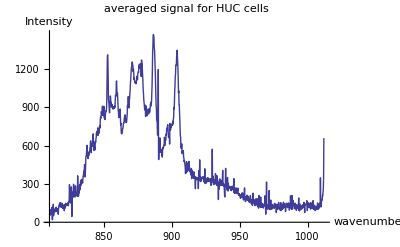

```mathematica
ListLinePlot[averagedHUV, AxesLabel->{"wavenumber","Intensity"},PlotLabel->"averaged signal for HUC cells"]
```

## Subtracting the mean

```mathematica
allmgh=Flatten[List[(Flatten[Drop[#,None,1]])&/@{MGH1,MGH2,MGH3,MGH4,MGH5,MGH6,MGH7,MGH8,MGH9}],1];
allhuc=Flatten[List[(Flatten[Drop[#,None,1]])&/@{HUC1,HUC2,HUC3,HUC4,HUC5,HUC6,HUC7,HUC8,HUC9}],1];
```

```mathematica
alldatai=Join[allmgh,allhuc];
```

```mathematica
For[i=1;listmaall={},i≤Length[alldatai],i++,listmaall=Append[listmaall,alldatai[[i]]-Mean[alldatai[[i]]]]]
Dimensions[listmaall]
```

## Covariance Matrix, eigenvalues and eigenvectors

```mathematica
covariancematrix=Covariance[alldatai];
Dimensions[covariancematrix]
```

{1024,1024}

```mathematica
eigenvalues=Eigenvalues[N[covariancematrix]];
```

```mathematica
eigenvectors=Eigenvectors[N[covariancematrix]];
```

```mathematica
Length[eigenvalues]
```

1024

## feature matrix and PCA analysis

Using Kaiser criterion to select any component with an eigenvalue > 1, this means that the component is accounting for a greater variance than contributed by one variable therefore significant enough to keep

```mathematica
Module[{n},numberofeigenvalues={};
n=1;
While[n<=Length[eigenvalues],If[eigenvalues[[n]]>1, AppendTo[numberofeigenvalues,1],Break];n++];Print["number of eigenvectors to keep =",Total[numberofeigenvalues]]]
```

number of eigenvectors to keep =17

```mathematica
featurevector=eigenvectors[[1;;Total[numberofeigenvalues]]];
```

```mathematica
reduceddataset=featurevector.Transpose[listmaall];
```

each row corresponds to the principle components, each column is a signal from a different sample, the first 9 correspond to mgh cells, the last 9 correspond to huc cells
A plot of the first two principle components will require transposing the first two rows together

```mathematica
PC12=Transpose[{reduceddataset[[1]],reduceddataset[[2]]}];
```

the first component is the x and y value of the first mgh cell, the x-axis will correspond to PC1 and the y axis to PC2, separate the components into sets of 9 to distinguish mgh from huc

```mathematica
Length[PC12]
```

18

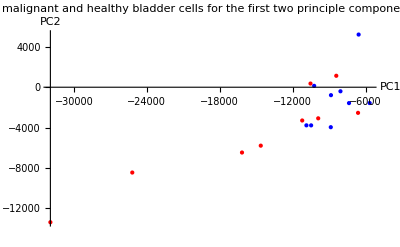

```mathematica
ListPlot[{PC12[[1;;9]],PC12[[10;;18]]},PlotStyle->{Red, Blue},PlotLegend->{"MGH","HUC"},LegendShadow->None,LegendSize->{0.5,0.4},LegendPosition->{1,-0.4},AxesLabel->{"PC1","PC2"},PlotLabel->"malignant and healthy bladder cells for the first two principle components"]
```

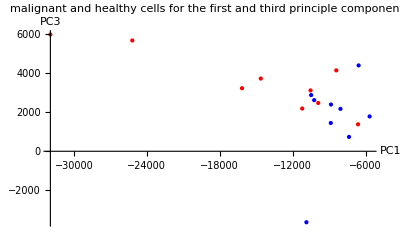

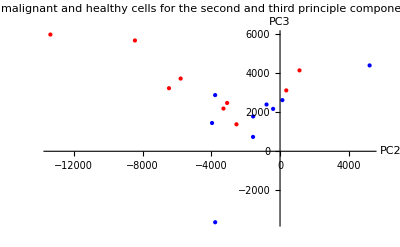

```mathematica
PC13:=Transpose[{reduceddataset[[1]],reduceddataset[[3]]}]
PC23:=Transpose[{reduceddataset[[2]],reduceddataset[[3]]}]
ListPlot[{PC13[[1;;9]],PC13[[10;;18]]},PlotStyle->{Red,Blue},PlotLegend->{"MGH","HUC"},LegendShadow->None,LegendSize->{0.4,0.3},LegendPosition->{1.1,-0.5},AxesLabel->{"PC1","PC3"},PlotLabel->"malignant and healthy cells for the first and third principle components",PlotRange->All]
ListPlot[{PC23[[1;;9]],PC23[[10;;18]]},PlotStyle->{Red,Blue},PlotLegend->{"MGH","HUC"},LegendShadow->None,LegendSize->{0.4,0.3},LegendPosition->{1.1,-0.5},AxesLabel->{"PC2","PC3"},PlotLabel->"malignant and healthy cells for the second and third principle components",PlotRange->All]
```

### 3-dimensional plot

```mathematica
PC123:=Transpose[{reduceddataset[[1]],reduceddataset[[2]],reduceddataset[[3]]}]
ListPlot3D[{PC123[[1;;9]],PC123[[10;;18]]},PlotStyle->{Red,Blue},AxesLabel->{"PC1","PC2","PC3"},PlotLabel->"3D plot using the first three principle components",PlotRange->All,Epilog->Inset[Framed[TableForm[{Style["MGH",15,Red],Style["HUC",15,Blue]}]],{Right,Bottom},{Right,Bottom}]]
```

-Graphics3D-

## Cross-validation

(http://dms.irb.hr/tutorial/tut_mod_eval_4.php, accessed on 11/12/2013) technique to estimate classifier error rates. classifier is generated using n-1 samples, and tested on single remaining case. This is repeated n times, so each case in the sample is used as a test case, and each time almost all the cases are used to design a classifier. The error rate is the number of errors on the single test cases, divided by n.
Over many sample sets, the leave-one-out estimate of the error will average to the true error rate. small samples of over 100 should be accurate.
Here the sample is only 18 therefore may be a biased error rate,  but for practice this should be ok. As the sample size is larger, computationally is more expensive but accuracy in error rates improve.

The first 9 samples should fall into MGH classification, the last 9 samples should fall into HUC classification. I will only use the first three eigenvectors because the first 3 principle components should be enough for classification

```mathematica
Module[{n,classificationdata,i,meanadjustedcv,meandatacv,covariancematrixcv,eigenvtcv,k,featurevectorcv,rdloo,meanadjustedlo,leftout,rdcd,PC12,PC13,PC23, plots12,plots13,plots23,p12,p13,p23},
n=1;
plots12={};
plots13={};
plots23={};

While[n<19, classificationdata=Drop[alldatai,{n}];
For[i=1;
meanadjustedcv={},i<=Length[classificationdata],i++,AppendTo[meanadjustedcv,classificationdata[[i]]-Mean[classificationdata]]];meandatacv=Mean[classificationdata];
covariancematrixcv=Covariance[classificationdata];
eigenvtcv=Eigenvectors[N[covariancematrixcv]];
featurevectorcv=eigenvtcv[[1;;3]];
rdcd=featurevectorcv.Transpose[meanadjustedcv];
PC12=Transpose[{rdcd[[1]],rdcd[[2]]}];
PC13=Transpose[{rdcd[[1]],rdcd[[3]]}];
PC23=Transpose[{rdcd[[2]],rdcd[[3]]}];

leftout=alldatai[[n]];
meanadjustedlo=leftout-meandatacv;
rdloo=featurevectorcv.meanadjustedlo;

If[n≤9,
p12=ListPlot[{PC12[[1;;8]],PC12[[9;;17]],{rdloo[[1]],rdloo[[2]]}},PlotStyle->{Red,Blue,Green},PlotLegend->{"MGH","HUC","unknown"},LegendPosition->{1,0.01},PlotRange->All,LegendShadow->None,LegendSize->{0.4,0.3},AxesLabel->{"PC1","PC2"},PlotLabel->"cross validation sample"<>ToString[n]"removed"];p13=ListPlot[{PC13[[1;;8]],PC13[[9;;17]],{rdloo[[1]],rdloo[[3]]}},PlotStyle->{Red,Blue,Green},PlotLegend->{"MGH","HUC","unknown"},LegendPosition->{1,0.01},PlotRange->All,LegendShadow->None,LegendSize->{0.4,0.3},AxesLabel->{"PC1","PC3"},PlotLabel->"cross validation sample"<>ToString[n]"removed"];p23=ListPlot[{PC23[[1;;8]],PC23[[9;;17]],{rdloo[[2]],rdloo[[3]]}},PlotStyle->{Red,Blue,Green},PlotLegend->{"MGH","HUC","unknown"},LegendPosition->{1,0.01},PlotRange->All,LegendShadow->None,LegendSize->{0.4,0.3},AxesLabel->{"PC2","PC3"},PlotLabel->"cross validation sample"<>ToString[n]"removed"];AppendTo[plots12,p12];AppendTo[plots13,p13];AppendTo[plots23,p23],

If[n≥10,
p12=ListPlot[{PC12[[1;;9]],PC12[[10;;17]],{rdloo[[1]],rdloo[[2]]}},PlotStyle->{Red, Blue, Green},PlotRange->All,PlotLegend->{"MGH","HUC","unknown"},LegendPosition->{1,0.01},LegendShadow->None,LegendSize->{0.4,0.3},AxesLabel->{"PC1","PC2"},PlotLabel->"cross validation sample"<>ToString[n]"removed"];p13=ListPlot[{PC13[[1;;9]],PC13[[10;;17]],{rdloo[[1]],rdloo[[3]]}},PlotStyle->{Red,Blue,Green},PlotLegend->{"MGH","HUC","unknown"},LegendPosition->{1,0.01},PlotRange->All,LegendShadow->None,LegendSize->{0.4,0.3},AxesLabel->{"PC1","PC3"},PlotLabel->"cross validation sample"<>ToString[n]"removed"];p23=ListPlot[{PC23[[1;;9]],PC23[[10;;17]],{rdloo[[2]],rdloo[[3]]}},PlotStyle->{Red,Blue,Green},PlotLegend->{"MGH","HUC","unknown"},LegendPosition->{1,0.01},PlotRange->All,LegendShadow->None,LegendSize->{0.4,0.3},AxesLabel->{"PC2","PC3"},PlotLabel->"cross validation sample"<>ToString[n]"removed"];
AppendTo[plots12,p12]AppendTo[plots13,p13];AppendTo[plots23,p23]]];n++];
ListAnimate[plots12,AnimationRunning->False]
ListAnimate[plots13,AnimationRunning->False]
ListAnimate[plots23,AnimationRunning->False]
]
```

```mathematica
TableForm[{{
```

```mathematica
n=1;

While[n<19, classificationdata=Drop[alldatai,{n}];
For[i=1;
meanadjustedcv={},i<=Length[classificationdata],i++,AppendTo[meanadjustedcv,classificationdata[[i]]-Mean[classificationdata]]];meandatacv=Mean[classificationdata];
covariancematrixcv=Covariance[classificationdata];
eigenvtcv=Eigenvectors[N[covariancematrixcv]];
featurevectorcv=eigenvtcv[[1;;3]];
rdcd=featurevectorcv.Transpose[meanadjustedcv];
PC12=Transpose[{rdcd[[1]],rdcd[[2]]}];n++]
```

```mathematica
Dimensions[PC12]
```

{17,2}

```mathematica
Length[PC12[[1]]]
```

2